# QMeSTools Showcase

## Load Package

```mathematica
(* Load the installed version of the package *)
Needs["QMeSderivation`"]
```

## Define the theory (a QCD truncation)

```mathematica
fRGEq = {
"Prefactor"->{1/2},
<|"type"->"Regulatordot", "indices"->{i,j}|>,
<|"type"->"Propagator", "indices"->{i,j}|>
};

fieldsQCD=<|
"bosonic"-> {
σ[p],(*sigma meson*)
Π[p,{a}],(*pions*)
 A[p,{v, c}](*gluon*)
},
 "fermionic"->{
{sb[p,{d,c}],s[p,{d,c}]},(*strange quark*)
{qb[p,{d,c,f}],q[p,{d,c,f}]},(*light quarks*)
{cb[p,{c}],c[p,{c}]}(*ghosts*)
}
|>;

TruncationQCD = {
{σ,σ},{Π,Π},{q,qb},{s,sb},{A,A},{c,cb},(* propagators *)
{qb,q,A},{cb,c,A},{sb,s,A},{A,A,A},{A,A,A,A},(* gluon sector scatterings *)
{qb,q,σ},{qb,q,Π},{qb,q,σ,σ},{qb,q,Π,Π},{qb,q,σ,Π},{qb,q,σ,σ,σ},{qb,q,σ,σ,Π},{qb,q,σ,Π,Π},{qb,q,Π,Π,Π}, (* quark-meson scatterings *)
 {σ,σ,σ},{σ,Π,Π},{σ,σ,σ,σ},{σ,σ,Π,Π},{Π,Π,Π,Π}(* meson scatterings *)
};

SetupfRGQCD= <|"MasterEquation"->fRGEq,
"FieldSpace"->fieldsQCD,
"Truncation"->TruncationQCD
|>;
```

## FRG Equations: Four-Quark vertex

### Derive flow equation of four-quark vertex

```mathematica
DerivativeListqbqqbq= {qb[p,{d4,c4,f4}],q[-p,{d3,c3,f3}],qb[p,{d2,c2,f2}],q[-p,{d1,c1,f1}]};
Diagramsqbqqbq=DeriveFunctionalEquation[SetupfRGQCD,DerivativeListqbqqbq,"OutputLevel"->"SuperindexDiagrams"];
Diagramsqbqqbq//Length
```

400

### Reduce the number of diagrams by using the symmetries of the tensor structure and the t-channel configuration

```mathematica
ReduceIdenticalFlowDiagrams::usage
```

ReduceIdenticalFlowDiagrams[diagrams,derivativeList,symmetries]

Reduce a set of flow equations by matching identical topologies and/or by utilizing a given set of symmetries.
The user has to supply the list of derivatives (i.e. external legs in the diagrams). Then, the symmetries are specified in the following way:
symmetries = {
	{ {1, 3}, Minus},
	{ {2, 4}, Minus}
	{ {1, 3}, {2, 4}, Plus},
}
Here, two antisymmetries (as specified by the Minus) are given, which consist of a single cycle each (1,3) and (2,4). These integers refer to the legs as given in derivativeList (in order).
ReduceIdenticalFlowDiagrams does not construct all symmetries from the given ones - therefore, the full symmetry group needs to be specified. Therefore, we also supply the symmetry consisting of both cycles explicitly in the third line.

```mathematica
symmetries={
{{1,3},Plus},
{{2,4},Plus},
{{1,3},{2,4},Plus}
};
DiagramsqbqqbqReduced=ReduceIdenticalFlowDiagrams[Diagramsqbqqbq,DerivativeListqbqqbq,symmetries];
DiagramsqbqqbqReduced//Length
```

61

### Plot the resulting diagrams

```mathematica
PlotSuperindexDiagram::usage
```

PlotSuperindexDiagram[diagram, setup, options]

Plot a single superindex diagram. The first argument to this function is the diagram itself, the second one is a valid QMeS setup.
The diagram has to be a superindex diagram.

The options for the function PlotSuperindexDiagram are:
"ShowEdgeLabels" ->  False / True
	This option will toggle whether edges are plotted together with labels to identify them.
"EdgeStyle" ->  List
	Using this option, one can specify the edge styles of different propagators. e.g.,
		"EdgeStyle"->{q->Blue,A->Orange,Π->{Dashed,Thick},σ->{Dashed,Thick,Purple}}.

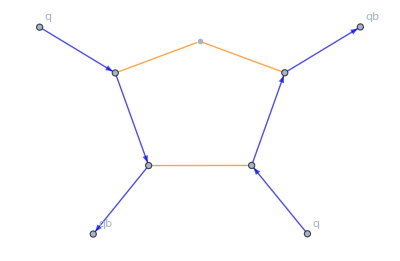
{4,-Graphics-}

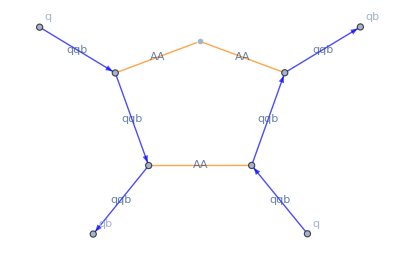
{4,-Graphics-}

```mathematica
PlotSuperindexDiagram[
DiagramsqbqqbqReduced[[1]],SetupfRGQCD,
"EdgeStyle"->{q->Blue,A->Orange,Π->{Dashed,Thick},σ->{Dashed,Thick,Purple}},
"ShowEdgeLabels"->False
]
PlotSuperindexDiagram[
DiagramsqbqqbqReduced[[1]],SetupfRGQCD,
"EdgeStyle"->{q->Blue,A->Orange,Π->{Dashed,Thick},σ->{Dashed,Thick,Purple}},
"ShowEdgeLabels"->True
]
```

```mathematica
PlotSuperindexDiagrams::usage
```

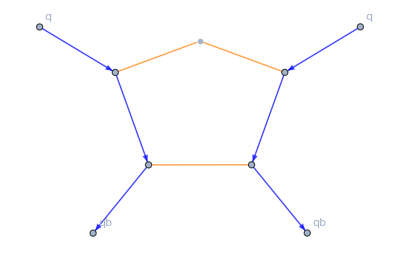
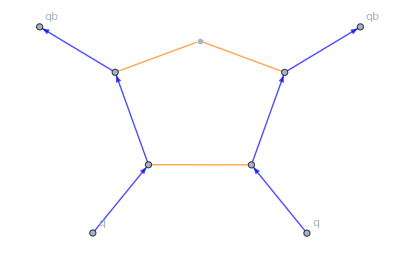
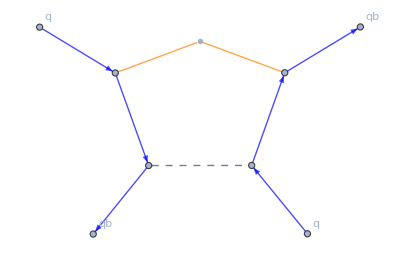
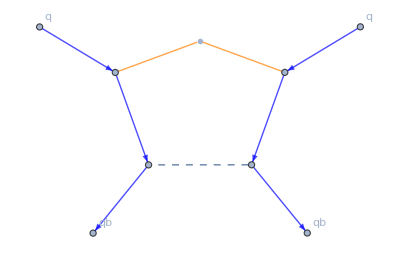
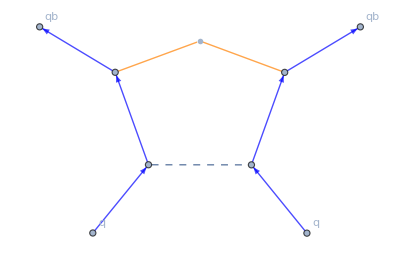
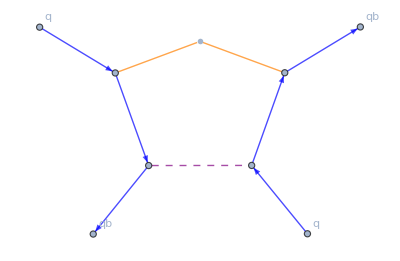
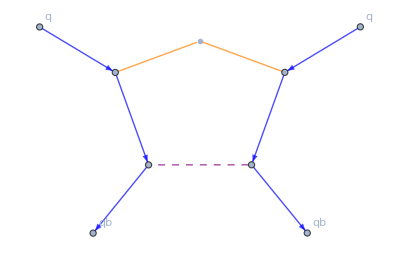
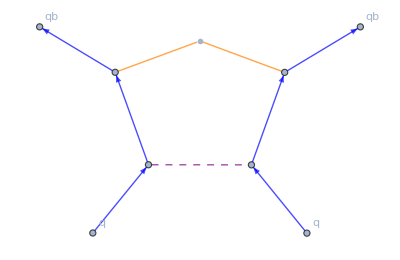
{{4,-Graphics-},{2,-Graphics-},{-2,-Graphics-},{4,-Graphics-},{2,-Graphics-},{-2,-Graphics-},{4,-Graphics-},{2,-Graphics-},{-2,-Graphics-},{-4,-Graphics-},{-4,-Graphics-},{-4,-Graphics-},{-4,-Graphics-},{-4,-Graphics-},{-4,-Graphics-},{-4,-Graphics-},{-4,-Graphics-},{-4,-Graphics-},{-4,-Graphics-},{-4,-Graphics-},{-4,-Graphics-},{-4,-Graphics-},{-4,-Graphics-},{-4,-Graphics-},{-4,-Graphics-},{-4,-Graphics-},{-4,-Graphics-},{4,-Graphics-},{2,-Graphics-},{-2,-Graphics-},{4,-Graphics-},{2,-Graphics-},{-2,-Graphics-},{4,-Graphics-},{2,-Graphics-},{-2,-Graphics-},{4,-Graphics-},{2,-Graphics-},{-2,-Graphics-},{4,-Graphics-},{2,-Graphics-},{-2,-Graphics-},{4,-Graphics-},{2,-Graphics-},{-2,-Graphics-},{4,-Graphics-},{-4,-Graphics-},{4,-Graphics-},{-4,-Graphics-},{4,-Graphics-},{-4,-Graphics-},{4,-Graphics-},{-4,-Graphics-},{-4,-Graphics-},{-4,-Graphics-},{-4,-Graphics-},{-4,-Graphics-},{-2,-Graphics-},{-2,-Graphics-},{-2,-Graphics-},{-2,-Graphics-}}

```mathematica
PlotSuperindexDiagrams[
DiagramsqbqqbqReduced,SetupfRGQCD,
"EdgeStyle"->{q->Blue,A->Orange,Π->{Dashed,Thick},σ->{Dashed,Thick,Purple},c->Dotted},
"ShowEdgeLabels"->False
]
```

## FRG Equations: Three-gluon vertex

### Derive flow equation of three-gluon vertex

```mathematica
DerivativeListAAA= {A[p1,{v1,c1}],A[p2,{v3,c3}],A[p3,{v3,c3}]};
DiagramsAAA=DeriveFunctionalEquation[SetupfRGQCD,DerivativeListAAA,"OutputLevel"->"SuperindexDiagrams"];
DiagramsAAA//Length
```

48

### Reduce the number of diagrams on the symmetric point

```mathematica
ReduceIdenticalFlowDiagrams::usage
```

ReduceIdenticalFlowDiagrams[diagrams,derivativeList,symmetries]

Reduce a set of flow equations by matching identical topologies and/or by utilizing a given set of symmetries.
The user has to supply the list of derivatives (i.e. external legs in the diagrams). Then, the symmetries are specified in the following way:
symmetries = {
	{ {1, 3}, Minus},
	{ {2, 4}, Minus}
	{ {1, 3}, {2, 4}, Plus},
}
Here, two antisymmetries (as specified by the Minus) are given, which consist of a single cycle each (1,3) and (2,4). These integers refer to the legs as given in derivativeList (in order).
ReduceIdenticalFlowDiagrams does not construct all symmetries from the given ones - therefore, the full symmetry group needs to be specified. Therefore, we also supply the symmetry consisting of both cycles explicitly in the third line.

```mathematica
symmetries={
{{1,2},Plus},
{{2,3},Plus},
{{3,1},Plus},
{{1,2,3},Plus},
{{3,2,1},Plus}
};
DiagramsAAAReduced=ReduceIdenticalFlowDiagrams[DiagramsAAA,DerivativeListAAA,symmetries];
DiagramsAAAReduced//Length
```

5

### Plot the resulting diagrams

```mathematica
PlotSuperindexDiagram::usage
```

PlotSuperindexDiagram[diagram, setup, options]

Plot a single superindex diagram. The first argument to this function is the diagram itself, the second one is a valid QMeS setup.
The diagram has to be a superindex diagram.

The options for the function PlotSuperindexDiagram are:
"ShowEdgeLabels" ->  False / True
	This option will toggle whether edges are plotted together with labels to identify them.
"EdgeStyle" ->  List
	Using this option, one can specify the edge styles of different propagators. e.g.,
		"EdgeStyle"->{q->Blue,A->Orange,Π->{Dashed,Thick},σ->{Dashed,Thick,Purple}}.

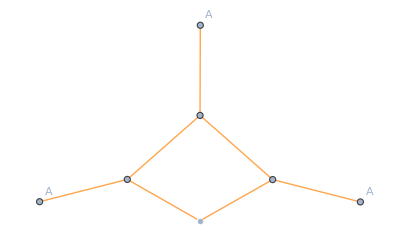
{-3,-Graphics-}

```mathematica
PlotSuperindexDiagram[
DiagramsAAAReduced[[1]],SetupfRGQCD,
"EdgeStyle"->{q->Blue,A->Orange,Π->{Dashed,Thick},σ->{Dashed,Thick,Purple}},
"ShowEdgeLabels"->False
]
```

```mathematica
PlotSuperindexDiagrams::usage
```

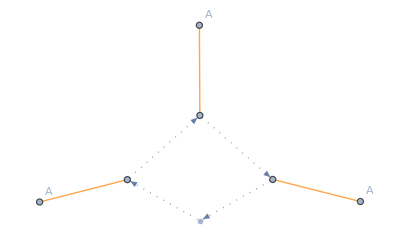
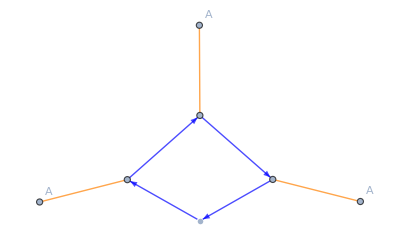
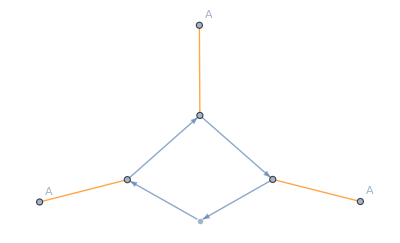
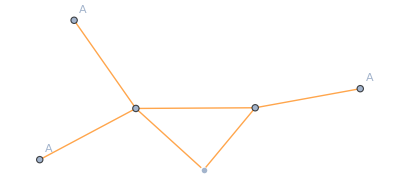
{{-3,-Graphics-},{-6,-Graphics-},{-6,-Graphics-},{-6,-Graphics-},{3,-Graphics-}}

```mathematica
PlotSuperindexDiagrams[
DiagramsAAAReduced,SetupfRGQCD,
"EdgeStyle"->{q->Blue,A->Orange,Π->{Dashed,Thick},σ->{Dashed,Thick,Purple},c->Dotted},
"ShowEdgeLabels"->False
]
```